```mathematica
sumIntDigits[n_, b_]:=Total[IntegerDigits[n, b]]
```

```mathematica
sumIntDigits[17, 10]
```

8

```mathematica
sumIntDigits[10, 2]
```

2

```mathematica
expSumList[n_ ,b_, p_]:=Accumulate[Exp[2.0*Pi*I*sumIntDigits[#, b]/p]&/@Range[n]]
```

```mathematica
Range[4.23123]
```

{1,2,3,4}

```mathematica
expSumList[1000,10, 4];
```

```mathematica
visualizer[n_, b_, p_]:=ListLinePlot[ReIm /@ expSumList[n,b, p]]
```

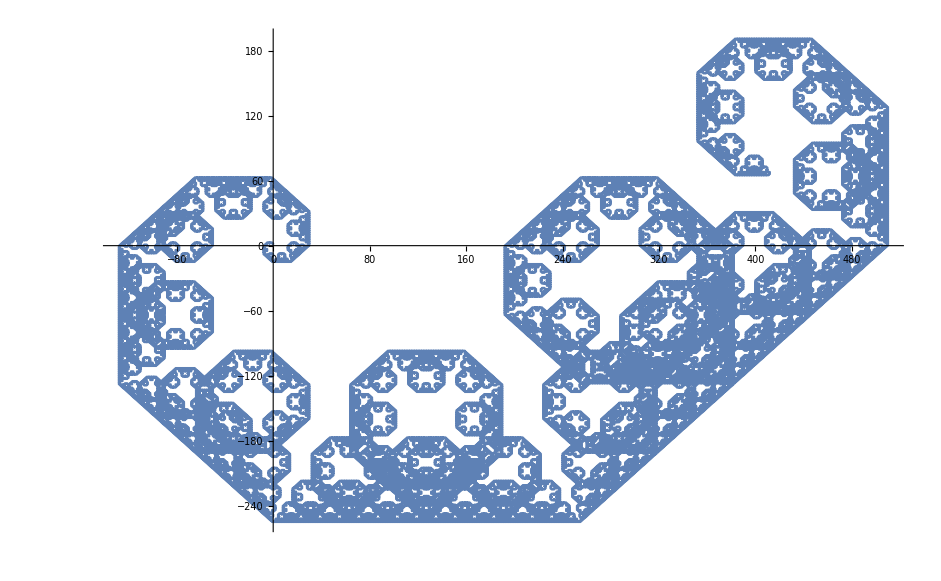

```mathematica
visualizer[100000, 2, 4]
```

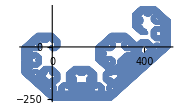

```mathematica
Show[%430,ImageSize->Small]
```

```mathematica
(* Table of some integer visualizations in base 10, varying by param p *)
```

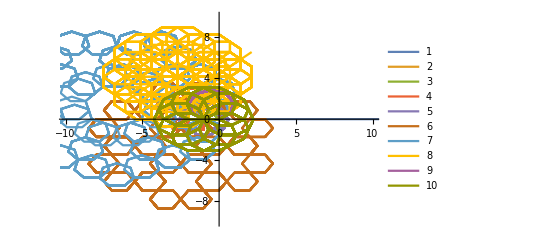

```mathematica
ListLinePlot[(ReIm /@ expSumList[1000, 10, #])& /@ Range[10],PlotRange->{{-10, 10},{-10, 10}}, PlotLegends->Range[10]]
```

```mathematica
(* Table of some integer visualizations in base 10, varying by param n *)
```

```mathematica
Manipulate[list = ReIm /@ expSumList[10000, 2, 4];
maxRange = Max[Abs[list]];
ListLinePlot[Take[list,t],PlotRange->{{-maxRange, maxRange},{-maxRange, maxRange}}], {t, 1, 10000, 1}]
```

```mathematica
Manipulate[list = ReIm /@ expSumList[10000, 2, 1/Sqrt[3]];
partialList = Take[list, t];
maxRange = Max[Abs[partialList]]*1.1;
Graphics[Line[partialList], PlotRange->{{-maxRange, maxRange},{-maxRange, maxRange}}, Axes->True], {t, 2, 10000, 10}]
```

```mathematica
(* Table of some integer visualizations varying in base *)
```

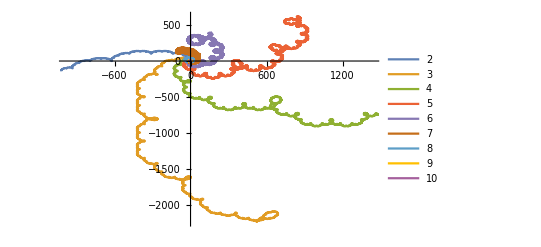

```mathematica
ListLinePlot[(ReIm /@ expSumList[10000, #, 10])& /@ Range[2,10], PlotLegends->Range[2,10]]
```

```mathematica
randomRealTable = RandomReal[{1,3}, 15]  (* 15 random real numbers ranging from 0 to 25 *)
```

{2.34495,2.22422,1.8063,1.01154,1.16227,1.99244,1.78697,1.20154,2.78018,1.56881,1.70973,1.0152,1.43945,1.21861,1.97841}

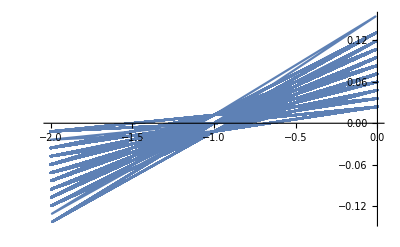
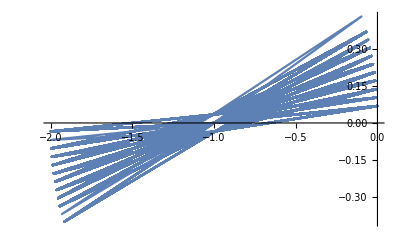
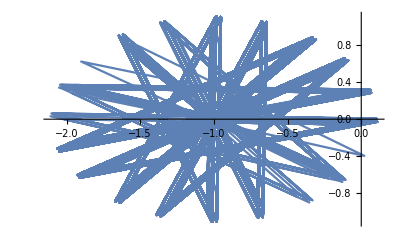
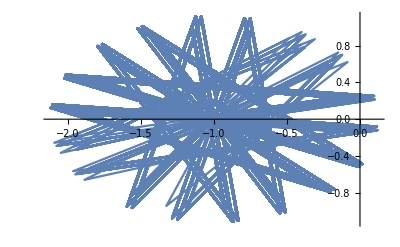
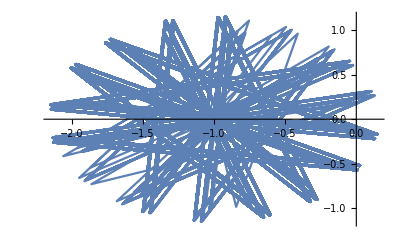
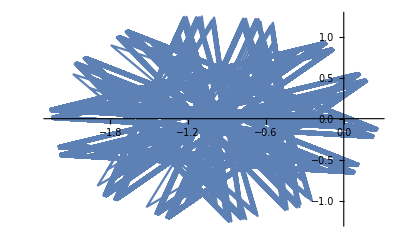
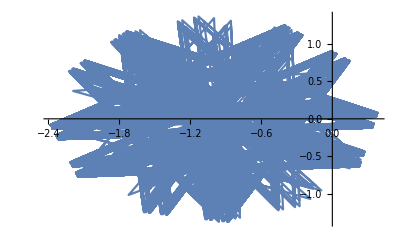
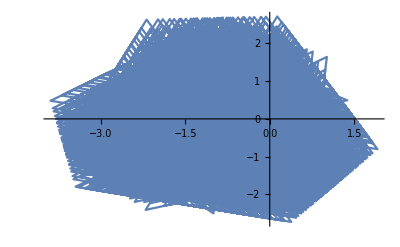
{{-Graphics-,1.99244},{-Graphics-,1.97841},{-Graphics-,2.22422},{-Graphics-,1.8063},{-Graphics-,1.78697},{-Graphics-,2.34495},{-Graphics-,1.70973},{-Graphics-,1.56881},{-Graphics-,2.78018},{-Graphics-,1.43945},{-Graphics-,1.21861},{-Graphics-,1.20154},{-Graphics-,1.16227},{-Graphics-,1.0152},{-Graphics-,1.01154}}

```mathematica
Sort[Table[{ListLinePlot[ReIm /@ expSumList[10000, 2, x]], x}, {x, randomRealTable}]]
```

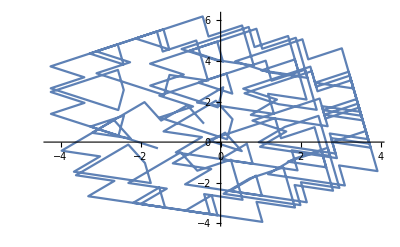

```mathematica
visualizer[250, 2, Pi]
```

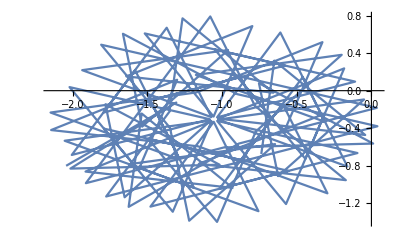

```mathematica
visualizer[100, 10, GoldenRatio]
```

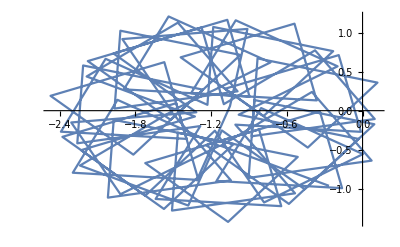

```mathematica
visualizer[100, 10, Sqrt[2]]
```